336.7

CI= (3.1451×10^-6±2.89671×10^-9) a=336.7

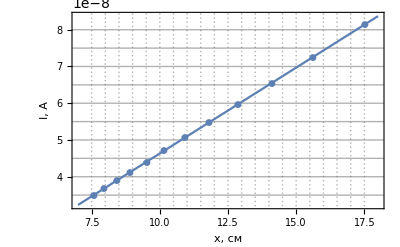

```mathematica
Needs["ErrorBarPlots`"]
U0=67/150*3;
R2=10*1000;
R1=1/1000*R2;
R0=475;
a=Mean[{335,338.4}]
M1={{16, 17.5}, {18, 15.6}, {20, 14.1}, {22, 12.85}, {24, 11.8}, {26, 10.9}, {28, 10.15}, {30, 9.5}, {32, 8.9}, {34, 8.4}, {36, 7.95}, {38, 7.55}};
CalculateI[R_]:=U0*R1/R2*1/(R*1000+R0);
M1=ArrayPad[M1,{0,1}];
For[i=1,i≤12,i++,
M1[[i,3]] = CalculateI[M1[[i,1]]];]
M1=ArrayPad[M1,{1,0}];
M1[[1,2]] = "R, кОм";
M1[[1,3]] = "x, см";
M1[[1,4]] = "I, А";
M2=M1;
For[i=2,i≤13,i++,
M2[[i,4]] = N[CalculateI[M2[[i,2]]]];]
Export["M1.pdf",Grid[M2[[1;;13,2;;4]], Frame->All ]];

xError = 0.1;
xErrorsValues = Table[xError, 12];
yErrorsValues = Table[0,12];
For[i = 2, i<14, i++,
yErrorsValues [[i-1]]=(0.5*U0)/100*M1[[i,4]];]
errorValues = Table[0,12];
For[i=1,i<13,i++,
errorValues[[i]] = ErrorBar[xErrorsValues[[i]],yErrorsValues[[i]]];]
PlotPart=M1[[2;;13,3;;4]];
ApproximationLine = LinearModelFit[PlotPart,x,x];
Normal[ApproximationLine];
CI=2*a*ApproximationLine["BestFitParameters"][[2]];
sigmaCI =Sqrt[ D[2*da*ApproximationLine["BestFitParameters"][[2]], da]^2*sigmaA^2+D[2*a*tn, tn]^2*(ApproximationLine["ParameterErrors"][[2]])^2];
Print["CI= (",CI,"±", sigmaCI,") a=", a]
PlotPart=Partition[Riffle[PlotPart,errorValues],2];
Show[ErrorListPlot[PlotPart, PlotRange->Automatic, PlotTheme->"Detailed" ,PlotMarkers->Automatic, GridLines->All], Plot[ApproximationLine[x],{x,7,18} ], PlotRange->Automatic,FrameLabel->{{RawBoxes[RowBox[{"I",","," ","А"}]],None},{RawBoxes[RowBox[{"x",","," ","см"}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}, ImageSize->Full]
```

```mathematica
0
```

```mathematica
MX={{23.3, 12, 7.6}, {18.9, 9.5, 6.1}};
MX=ArrayPad[MX,{{0,1},{0,0}}];
For[i = 1, i<4, i++,
MX[[3,i]]=Log[MX[[1,i]]/MX[[2,i]]];
]
MXP = MX;
MXP=ArrayPad[MXP,{{0,0},{1,0}}];
MXP[[1,1]]="X_n, см";
MXP[[2,1]]="X_(n + 1), см";
MXP[[3,1]]="Θ";
Export["M2.pdf", Grid[MXP, Frame->All]];
ΘMid=Mean[MX[[3]]]
MeanDeviation[MX[[3]]]
```

0.220922

0.00846195

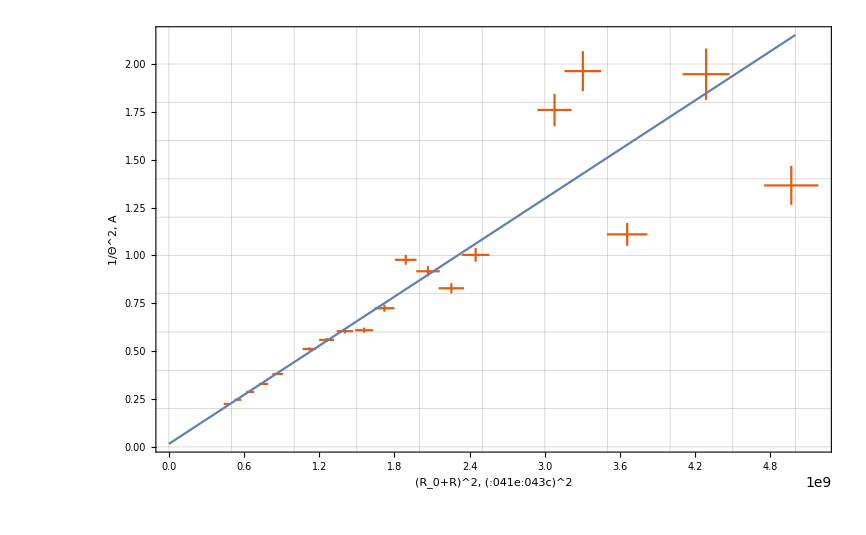

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0156951 | 0.0109501 | 1.43333 | 0.194877
x | 4.27255×10^-10 | 1.15744×10^-11 | 36.9139 | 2.78306×10^-9

7224.75

208.587

```mathematica
M3={{21, 13.2, 1.6}, {23, 12, 1.6}, {25, 11, 1.7}, {27, 10.3, 1.8}, {29, 9.6, 1.9}, {31, 9, 2}, {33, 8.5, 2.1}, {35, 8, 2.1}, {37, 7.6, 2.1}, {39, 7.2, 2}, {41, 6.8, 2.1}, {43, 6.6, 2.4}, {45, 6.25, 2.2}, {47, 6, 2}, {49, 5.7, 2.1}, {55, 5.1, 2.4}, {57, 4.9, 2.4}, {60, 4.65, 1.8}, {65, 4.3, 2.1}, {70, 4, 1.7}};
M3=ArrayPad[M3, {{0,0},{0,3}}];
ClearAll[M3P];
M3P=M3;
For[i = 1, i<21,i++,
M3[[i,4]]=Log[M3[[i,2]]/M3[[i,3]]];
M3[[i,6]]=1/M3[[i,4]]^2;
M3[[i,5]]=(M3[[i,1]]*1000+R0)^2;
]
For[i = 1, i<21,i++,
M3P[[i,4]]=N[Log[M3P[[i,2]]/M3P[[i,3]]]];
M3P[[i,4]]=N[M3P[[i,4]]];
M3P[[i,6]]=N[1/M3P[[i,4]]^2, 1];
M3P[[i,6]]=N[1/M3P[[i,4]]^2, 1];
M3P[[i,5]]=(M3P[[i,1]]*1000+R0)^2;
]
M3P=ArrayPad[M3P,{{1,0},{0,0}}];
M3P[[1,1]]="R, кОм";
M3P[[1,2]]="x_n, см";
M3P[[1,3]]="x_(n + 1), см";
M3P[[1,4]]="Θ";
M3P[[1,5]]="(R+R_0)^2, (:041e:043c)^2";
M3P[[1,6]]="1/Θ^2";
Export["M3P.pdf",Grid[M3P, Frame->All]];
ResistorError[R_]:=0.2+6*10^-6*(Rk/R-1);
Rk=99999.9;
RError = Table[0,20];
Theta=Table[0,20];
errorValues2 = Table[0,20];
Sqrt[D[(1/Log[(xn/xn1)])^2,xn]^2*sxn^2+D[(1/Log[xn/xn1])^2,xn1]^2*sxn1^2];
For[i=1,i<21,i++,
RError[[i]]=(ResistorError[M3[[i,1]]]*Sqrt[M3[[i,5]]])^2;
Theta[[i]]=Sqrt[(4(0.2/M3[[i,2]])^2)/(M3[[i,2]]^2 Log[M3[[i,2]]/M3[[i,3]]]^6)+(4(0.2/M3[[i,3]])^2)/(M3[[i,2]]^2 Log[M3[[i,2]]/M3[[i,3]]]^6)];
errorValues2[[i]]=ErrorBar[RError[[i]],Theta[[i]]];
]
Grid[errorValues2];
PlotPart2 = Part[M3,1;;20,5;;6];
Grid[PlotPart2];
ApproximationLine2 = LinearModelFit[PlotPart2[[1;;9]],x,x];
PlotPart2=Partition[Riffle[PlotPart2,errorValues2],2];
Show[ErrorListPlot[PlotPart2,PlotTheme->"Scientific", GridLines->All, PlotMarkers->""],Plot[ApproximationLine2[x],{x,0,5*10^9}], PlotRange->Automatic,FrameLabel->{{RawBoxes[RowBox[{"1/Θ^2",","," ","А"}]],None},{RawBoxes[RowBox[{"(R_0+R)^2",","," ","(:041e:043c)^2"}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
Export["M3P.pdf",ApproximationLine2["ParameterTable"]];
ApproximationLine2["ParameterTable"]
Rcr=Sqrt[1/ApproximationLine2["BestFitParameters"][[2]]]/(2*Pi)-R0
σRcr=Sqrt[D[1/(2*Pi*Sqrt[ApproximationLine2["BestFitParameters"][[2]]])]^2*((ApproximationLine2["ParameterErrors"][[2]])/(ApproximationLine2["BestFitParameters"][[2]]))^2]
```

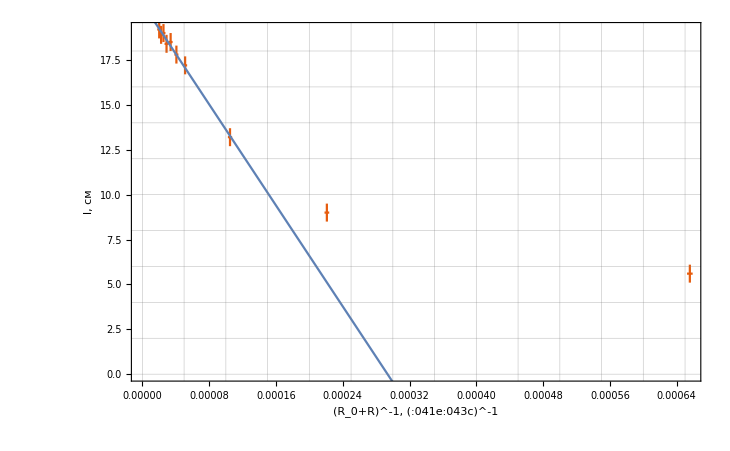

| Estimate | Standard Error | t-Statistic | P-Value
1 | 20.6567 | 0.112088 | 184.29 | 1.72221×10^-12
x | -70335.6 | 2309.35 | -30.4569 | 8.31461×10^-8

```mathematica
M4={{50, 19.2}, {45, 18.9}, {40, 19}, {35, 18.4}, {30, 18.5}, {25, 17.8}, {20, 17.2}, {10, 13.2}, {5, 9}, {2, 5.6}};
M4=ArrayPad[M4,{{0,0},{0,1}}];
M4P=M4;
For[i=1,i<11,i++,
M4[[i,3]]=1/(M4[[i,1]]*1000-R0);
M4P[[i,3]]=ScientificForm[N[M4[[i,3]]]];
]
M4P=ArrayPad[M4P,{{1,0},{0,0}}];
M4P[[1,1]]="R, кОм";
M4P[[1,2]]="l, см";
M4P[[1,3]]="1/(R - SubscriptBox[R, 0]), 1/Ом";
Export["M4.pdf", Grid[M4P, Frame->All]];
PlotPart3=M4[[1;;10,2;;3]];
PlotPart3=PlotPart3.({{0, 1}, {1, 0}});
lErrors=Table[0.5,10];
RErrors=Table[0,10];
errorValues3=Table[0,10];
For[i=1,i<11,i++,
RErrors[[i]]=Sqrt[D[1/(M4[[i,2]]*1000-R0)]^2*(ResistorError[M4[[i,2]]]/100*M4[[i,2]])^2];
errorValues3[[i]]=ErrorBar[RErrors[[i]],lErrors[[i]]];
]
ApproximationLine3=LinearModelFit[PlotPart3[[1;;8,All]],x,x];
PlotPart3=Partition[Riffle[PlotPart3,errorValues3],2];
Show[ErrorListPlot[PlotPart3, PlotMarkers->"", PlotRange->Automatic, PlotTheme->"Scientific",GridLines->All],Plot[ApproximationLine3[x],{x,0,19}], FrameLabel->{{RawBoxes[RowBox[{"l",","," ","см"}]],None},{RawBoxes[RowBox[{"(R_0+R)^-1",","," ","(:041e:043c)^-1"}]],None}}]
ApproximationLine3["ParameterTable"]
Export["M4P.pdf", ApproximationLine3["ParameterTable"]];
```

```mathematica
Normal[ApproximationLine3]
```

```mathematica
Solve[30==(20.656682430762903-70335.61679420838 (x+R0)^-1)*E,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→6836.17}}

```mathematica
Solve[lm==(a-b*(x+r)^-1)*E,x][[1]][[1]]
```

x→(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm)

```mathematica
ClearAll[a];
ClearAll[b];
ClearAll[r];
ClearAll[lm];
D[(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm),b]
D[(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm),a]
D[(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm),lm]
lm = 300;
a=20.7;
b = 70335.6;
r=R0;
```

ⅇ/(a ⅇ-lm)

-(ⅇ r)/(a ⅇ-lm)-(ⅇ (b ⅇ-a ⅇ r+lm r))/(a ⅇ-lm)^2

r/(a ⅇ-lm)+(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm)^2

```mathematica
e1=ⅇ/(a ⅇ-lm);
```

```mathematica
e2=-(ⅇ r)/(a ⅇ-lm)-(ⅇ (b ⅇ-a ⅇ r+lm r))/(a ⅇ-lm)^2;
```

```mathematica
e3=r/(a ⅇ-lm)+(b ⅇ-a ⅇ r+lm r)/(a ⅇ-lm)^2;
Sqrt[e1^2*2309.4^2+e2^2*0.112^2+e3^2*0.05^2]
```

253.808

```mathematica
ClearAll[a];
c=2*10^-6;
```

```mathematica
c=2*10^-6;
U0=67/150*3;
lm=30;
a=Mean[{335,338.4}]
R1=R2/30;
Cq=N[2*a*R1/R2*(U0*c)/lm]
ClearAll[U0];
ClearAll[lm];
ClearAll[a];
e1=D[2*a*R1/R2*(U0*c)/lm,a];
e2=D[2*a*R1/R2*(U0*c)/lm,U0];
e3=D[2*a*R1/R2*(U0*c)/lm,lm];
a=Mean[{335,338.4}];
lm=30;
U0=67/150*3;
ClearAll[sigmaA];
sigmaA =Sqrt[D[MeanDeviation[{335,338.4}]]^2*((0.05)+(0.05))^2];
sigmaCq = N[Sqrt[e1^2*sigmaA^2+e2^2*0.5^2+e3^2*0.05^2]];
Print[Cq,"±",sigmaCq]
```

336.7

2.00524×10^-6

2.00524×10^-6±7.4823×10^-7

```mathematica
2*MeanDeviation[{335,338.4}]*1/30*(1.34*2*10^-6)/30
```

1.01244×10^-8